```mathematica
((x-1)(x-4)(x-6))/-24
```

-1/24 (-6+x) (-4+x) (-1+x)

```mathematica
Expand[-1/24 (-6+x) (-4+x) (-1+x)]
```

1-(17 x)/12+(11 x^2)/24-x^3/24

```mathematica
--------------------------------------------------
```

```mathematica
((x-0)(x-4)(x-6))/-15
```

-1/15 (-6+x) (-4+x) x

```mathematica
Expand[-1/15 (-6+x) (-4+x) x]
```

-(8 x)/5+(2 x^2)/3-x^3/15

```mathematica
------------------------------------------------------------
```

```mathematica
((x-0)(x-1)(x-6))/-24
```

-1/24 (-6+x) (-1+x) x

```mathematica
Expand[-1/24 (-6+x) (-1+x) x]
```

-x/4+(7 x^2)/24-x^3/24

```mathematica
---------------------------------------------------------------
```

```mathematica
((x-0)(x-1)(x-4))/-60
```

-1/60 (-4+x) (-1+x) x

```mathematica
Expand[-1/60 (-4+x) (-1+x) x]
```

-x/15+x^2/12-x^3/60

```mathematica
-------------------------------------------------------------
```

```mathematica
1-(17 x)/12+(11 x^2)/24-x^3/24-(8 x)/5+(2 x^2)/3-x^3/15-x/4+(7 x^2)/24-x^3/24-x/15+x^2/12-x^3/60
```

1-(10 x)/3+(3 x^2)/2-x^3/6

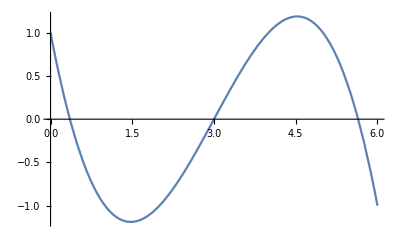

```mathematica
Plot[1-(10 x)/3+(3 x^2)/2-x^3/6,{x,0,6}]
```

```mathematica
f[x_]:=1-(10 x)/3+(3 x^2)/2-x^3/6
```

```mathematica
f[2]
```

-1

```mathematica
Clear[f]
```

```mathematica
-------------------------------------------------------
```

```mathematica
(4x(x-2)(x-4)(x-5))/-3
```

-4/3 (-5+x) (-4+x) (-2+x) x

```mathematica
Expand[-4/3 (-5+x) (-4+x) (-2+x) x]
```

(160 x)/3-(152 x^2)/3+(44 x^3)/3-(4 x^4)/3

```mathematica
--------------------------------------------------------
```

```mathematica
(x(x-1)(x-4)(x-5))/4
```

1/4 (-5+x) (-4+x) (-1+x) x

```mathematica
Expand[1/4 (-5+x) (-4+x) (-1+x) x]
```

-5 x+(29 x^2)/4-(5 x^3)/2+x^4/4

```mathematica
------------------------------------------------
```

```mathematica
(11x(x-1)(x-2)(x-5))/-3
```

-11/3 (-5+x) (-2+x) (-1+x) x

```mathematica
Expand[-11/3 (-5+x) (-2+x) (-1+x) x]
```

(110 x)/3-(187 x^2)/3+(88 x^3)/3-(11 x^4)/3

```mathematica
------------------------------------------------
```

```mathematica
(160 x)/3-(152 x^2)/3+(44 x^3)/3-(4 x^4)/3-5 x+(29 x^2)/4-(5 x^3)/2+x^4/4+(110 x)/3-(187 x^2)/3+(88 x^3)/3-(11 x^4)/3
```

85 x-(423 x^2)/4+(83 x^3)/2-(19 x^4)/4

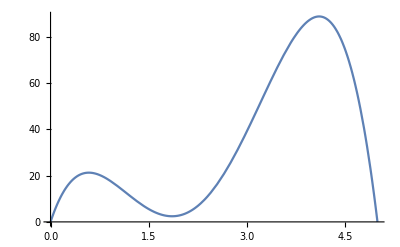

```mathematica
Plot[85 x-(423 x^2)/4+(83 x^3)/2-(19 x^4)/4,{x,0,5}]
```

```mathematica
f[x_]:=85 x-(423 x^2)/4+(83 x^3)/2-(19 x^4)/4
```

```mathematica
f[3]
```

39

```mathematica
D[(1/(1+x^2)), x]
```

-(2 x)/((1+x^2)^2)

```mathematica
D[(-(2 x)/((1+x^2)^2)), x]
```

(8 x^2)/((1+x^2)^3)-2/((1+x^2)^2)

```mathematica
Simplify[(8 x^2)/((1+x^2)^3)-2/((1+x^2)^2)]
```

(-2+6 x^2)/((1+x^2)^3)

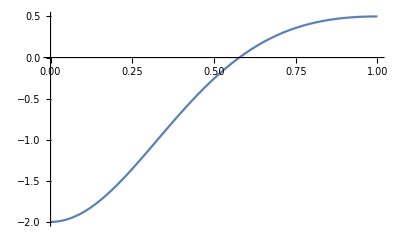

```mathematica
Plot[(-2+6 x^2)/((1+x^2)^3),{x,0,1}]
```

```mathematica
Clear(f)
```

Clear f

```mathematica
Clear[f]
```

```mathematica
f[x_]:=1/(1+x^2)
1/7
```

1/7

```mathematica
N[1/7]
```

0.142857

```mathematica
Table[f[x],{2,0,1}]
```

Table::itraw: Raw object 2 cannot be used as an iterator.

Table[f[x],{2,0,1}]

```mathematica
Range[1,2]
```

{1,2}

```mathematica
Table[f[x],{x,0,1,1/7}]
```

{1,49/50,49/53,49/58,49/65,49/74,49/85,1/2}

```mathematica
Sort[{1,49/50,49/53,49/58,49/65,49/74,49/85,1/2}]
```

{1/2,49/85,49/74,49/65,49/58,49/53,49/50,1}

```mathematica
Total[{1/2,49/85,49/74,49/65,49/58,49/53,49/50,1}]
```

1961192138/314201225

```mathematica
N[1961192138/314201225]
```

6.24183

```mathematica
1961192138/314201225*2
```

3922384276/314201225

```mathematica
3922384276/314201225-1-0.5
```

10.9837

```mathematica
NumberForm[10.983669584674598,16]
```

10.9836695846746

```mathematica
NumberForm[10.983669584674598,16]
```

10.9836695846746

```mathematica
10.9836695846746/14
```

0.784548

```mathematica
NumberForm[0.784547827476757,16]
```

0.784547827476757

```mathematica
Clear[f]
```

```mathematica
D[(√(1-t^2)), t]
```

-t/(√(1-t^2))

```mathematica
D[(-t/(√(1-t^2))), t]
```

-t^2/((1-t^2)^(3/2))-1/(√(1-t^2))

```mathematica
Simplify[-t^2/((1-t^2)^(3/2))-1/(√(1-t^2))]
```

-1/((1-t^2)^(3/2))

```mathematica
D[(-1/((1-t^2)^(3/2))), t]
```

-(3 t)/((1-t^2)^(5/2))

```mathematica
D[(-(3 t)/((1-t^2)^(5/2))), t]
```

-(15 t^2)/((1-t^2)^(7/2))-3/((1-t^2)^(5/2))

```mathematica
Simplify[-(15 t^2)/((1-t^2)^(7/2))-3/((1-t^2)^(5/2))]
```

-(3+12 t^2)/((1-t^2)^(7/2))

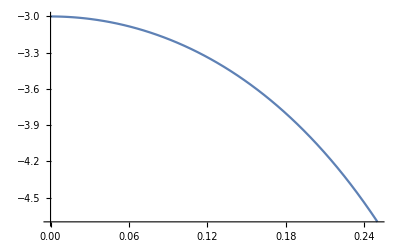

```mathematica
Plot[-(3+12 t^2)/((1-t^2)^(7/2)),{t,0,0.25}]
```